0.98

0.15

Eigenvalues at equilibrium points:

At (0,0) -> Eigenvalues: {0.18,0.1}

At (1,0) -> Eigenvalues: {-0.285,-0.1}

At (0,1) -> Eigenvalues: {-0.18,-0.0185}

At (1,1) -> Eigenvalues: {0.285,0.0185}

At internal equilibrium {β→0.843882,α→0.387097} -> Eigenvalues: {0.041501,-0.041501}

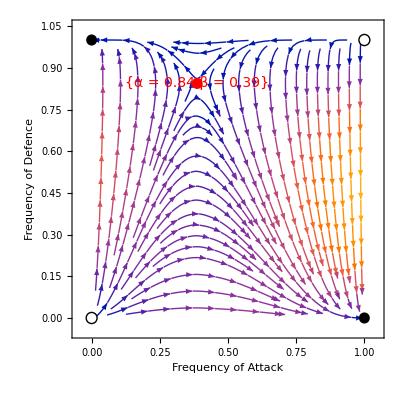

```mathematica
ClearAll["Global`*"]
(*Define the parameters*)
ba=0.79; (*Benefit of attack*)
bd=0.72; (*Benefit of defense*)
ca=0.69; (*Cost of attack*)
cd=0.54; (*Cost of defense*)
w=0.98 (*Loss to the defender*)
v=0.15(*Probability of successful defense*)
fs=0; (*Probability of catching attacker for attack*)
fu=0; (*Fine to attacker for an attack attempt*)

(*Define the replicator dynamics equations*)
f1=α(1-α) (-ca+ba-fs-ba*v*β-v*fu*β+v*fs*β);
f2=β(1-β) (bd-cd-bd*α+v*bd*α+v*w*α);

(*Compute the Jacobian matrix*)
J=D[{f2,f1},{{β,α}}];

(*Define the equilibrium points*)
equilibria={{0,0},{0,1},{1,0},{1,1}};

(*Compute eigenvalues at each equilibrium point and determine stability*)
Print["Eigenvalues at equilibrium points:"];

equilibriumMarkers=Table[eigs=Eigenvalues[J/. {α->eq[[2]],β->eq[[1]]}];
Print["At (",eq[[2]],",",eq[[1]],") -> Eigenvalues: ",eigs];
(*Check stability:If all eigenvalues are negative,it is stable (black filled).Otherwise,it is unstable (white filled).*)
If[AllTrue[eigs,#<0&],{Black,Disk[eq,0.02]},{White,Disk[eq,0.02],Black,Circle[eq,0.02]}],{eq,equilibria}];

(*Compute the correct internal equilibrium using the given formulas*)
internalEq={β->(ba-ca-fs)/(v*(ba-fs+fu)),α->(cd-bd)/(v*bd-bd+v*w)};

(*Check if internal equilibrium is valid (i.e.,within (0,1) range)*)
validInternalEq=0<internalEq[[1,2]]<1&&0<internalEq[[2,2]]<1;

If[validInternalEq,(*Compute eigenvalues at the internal equilibrium if it's valid*)eigsInternal=Eigenvalues[J/. internalEq];
Print["At internal equilibrium ",internalEq," -> Eigenvalues: ",eigsInternal];
(*Add the internal equilibrium point with red color and label*)AppendTo[equilibriumMarkers,{Red,Disk[{internalEq[[2,2]],internalEq[[1,2]]},0.02]}];
AppendTo[equilibriumMarkers,Text[Style[{"α = "<>ToString@NumberForm[internalEq[[1,2]],{3,2}],"β = "<>ToString@NumberForm[internalEq[[2,2]],{3,2}]},Red,14],{internalEq[[2,2]],internalEq[[1,2]]},{0,-1.2}]];,
(*Otherwise,notify that no valid internal equilibrium exists*)Print["No valid internal equilibrium in (0,1) range."]];

(*Stream plot with equilibrium points*)
StreamPlot[{f1,f2},{α,0,1},{β,0,1},PlotRange->{{-0.05,1.05},{-0.05,1.05}},FrameStyle->Directive[Black],FrameLabel->{Style["Frequency of Attack",22,FontFamily->"Arial",Black],Style["Frequency of Defence",22,FontFamily->"Arial",Black]},FrameTicksStyle->Directive[Black,FontFamily->"Arial",22],StreamStyle->{Black},Epilog->equilibriumMarkers]
```